# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\quantum_chaotic_channels\MG files\Spin chain\closed spin chain

```mathematica
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\QMB.wl"]
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\Chaometer.wl"]
```

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
BlochVector[ρ_]:=Tr[Pauli[#].ρ]&/@Range[3];
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]];
Braket[a_,b_]:=Conjugate[a].b;
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]];
Clear[SurvivalProbability];
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2;
```

```mathematica
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
```

```mathematica
LaunchKernels[8]
```

{Local (8),Local (8),Local (8),Local (8),Local (8),Local (8),Local (8),Local (8)}

# Sweep

## Hamiltonian

```mathematica
(*Set parameters in integrable region and compute Hamiltonian, and its eigenvalues and eigenvectors*)
L=3;
{hx,hz,J}={1,0.8,ConstantArray[1,L-1]};
```

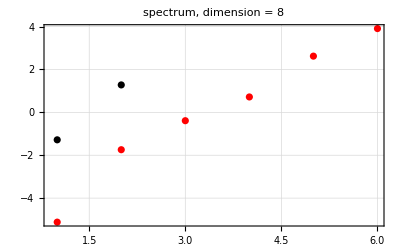

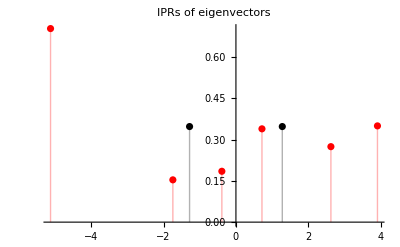

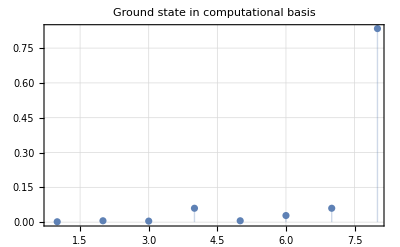

```mathematica
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
{EvenEigVals,evenEigenVecs}={eigVals[[#]],eigVecs[[#]]}&[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]];
OddEigVals=Complement[eigVals,EvenEigVals];
OddEigVecs=Complement[eigVecs,evenEigenVecs];
ListPlot[{EvenEigVals,OddEigVals},PlotRange->All,PlotTheme->"Detailed",PlotStyle->{Red,Black},ImageSize->400,PlotLabel->Style["spectrum, dimension = "<>ToString[2^L],25,Black]]
iprM=ParallelTable[Total[Quiet[Abs[i]^4]],{i,evenEigenVecs}];
iprm=ParallelTable[Total[Quiet[Abs[i]^4]],{i,OddEigVecs}];
ListPlot[{Transpose[{EvenEigVals,iprM}],Transpose[{OddEigVals,iprm}]},PlotRange->All,Filling->Axis,ImageSize->400,PlotStyle->{Red,Black},PlotLabel->Style["IPRs of eigenvectors",25,Black]]
ListPlot[Abs[eigVecs[[1]]]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->400,PlotLabel->Style["Ground state in computational basis",25,Black]]
```

## Channel

```mathematica
limit=Plot[0.25,{x,0,20.},PlotStyle->Directive[RGBColor[0.93,0.07,0.66],Dashed]];
```

```mathematica
L=3;
{hx,J}={1,ConstantArray[1,L-1]};
ψT={coherentstate[qubit[RandomReal[],RandomReal[]],L-1],RandomChainProductState[L-1],Normalize[Table[1,{i,2^(L-1)}]],Normalize[Table[If[0<=Mod[i,2^(L-1)]<=1,1,0],{i,2^(L-1)}]]};
tf=20.0;
(*test time for test image*)
t=1.5;
(*Set parameters in integrable region and compute Hamiltonian, and its eigenvalues and eigenvectors*)
hz=0.5;
styles={Style["Random Coherent state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Random product state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Uniform superposition, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Maximally entangled, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black]};
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
{EvenEigVals,evenEigenVecs}={eigVals[[#]],eigVecs[[#]]}&[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]];
(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplots={};
purities={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
choipurities={};
Do[
superOp=Superoperator[t,ψT[[i]],eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs[[i]],
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->800
]
];

AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];

AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];

,{t,0,tf,.1}];
AppendTo[listplots,
Show[{

ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","γ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];

AppendTo[purities,Show[{

ListPlot[Chop[choipurities],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];
,{i,4}];
testimage=Grid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],purities[[i]],figs[[i,Round[t*10]+1]]},{i,4}],Spacings->{5,5},Alignment->{Center,Center},Frame->All];
Export["testb_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>".png",testimage,ImageSize->2000];


(* --------- REGULAR OR CHAOTIC  ------------------*)
hz=3.0;
styles={Style["Random Coherent state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Random product state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Uniform superposition, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Maximally entangled, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black]};
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
{EvenEigVals,evenEigenVecs}={eigVals[[#]],eigVecs[[#]]}&[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]];
(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplots={};
purities={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
choipurities={};
Do[
superOp=Superoperator[t,ψT[[i]],eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs[[i]],
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->800
]
];

AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];

AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];

,{t,0,tf,.1}];
AppendTo[listplots,
Show[{

ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","γ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];

AppendTo[purities,Show[{

ListPlot[Chop[choipurities],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];
,{i,4}];
testimage=Grid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],purities[[i]],figs[[i,Round[t*10]+1]]},{i,4}],Spacings->{5,5},Alignment->{Center,Center},Frame->All];
Export["testb_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>".png",testimage,ImageSize->2000];
```

```mathematica
L=4;
{hx,J}={1,ConstantArray[1,L-1]};
ψT={coherentstate[qubit[RandomReal[],RandomReal[]],L-1],RandomChainProductState[L-1],Normalize[Table[1,{i,2^(L-1)}]],Normalize[Table[If[0<=Mod[i,2^(L-1)]<=1,1,0],{i,2^(L-1)}]]};
tf=20.0;
(*test time for test image*)
t=1.5;
(*Set parameters in integrable region and compute Hamiltonian, and its eigenvalues and eigenvectors*)
hz=0.5;
styles={Style["Random Coherent state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Random product state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Uniform superposition, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Maximally entangled, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black]};
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
{EvenEigVals,evenEigenVecs}={eigVals[[#]],eigVecs[[#]]}&[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]];
(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplots={};
purities={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
choipurities={};
Do[
superOp=Superoperator[t,ψT[[i]],eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs[[i]],
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->800
]
];

AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];

AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];

,{t,0,tf,.1}];
AppendTo[listplots,
Show[{

ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","γ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];

AppendTo[purities,Show[{

ListPlot[Chop[choipurities],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];
,{i,4}];
testimage=Grid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],purities[[i]],figs[[i,Round[t*10]+1]]},{i,4}],Spacings->{5,5},Alignment->{Center,Center},Frame->All];
Export["testb_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>".png",testimage,ImageSize->2000];


(* --------- REGULAR OR CHAOTIC  ------------------*)
hz=3.0;
styles={Style["Random Coherent state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Random product state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Uniform superposition, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Maximally entangled, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black]};
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
{EvenEigVals,evenEigenVecs}={eigVals[[#]],eigVecs[[#]]}&[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]];
(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplots={};
purities={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
choipurities={};
Do[
superOp=Superoperator[t,ψT[[i]],eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs[[i]],
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->800
]
];

AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];

AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];

,{t,0,tf,.1}];
AppendTo[listplots,
Show[{

ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","γ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];

AppendTo[purities,Show[{

ListPlot[Chop[choipurities],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];
,{i,4}];
testimage=Grid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],purities[[i]],figs[[i,Round[t*10]+1]]},{i,4}],Spacings->{5,5},Alignment->{Center,Center},Frame->All];
Export["testb_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>".png",testimage,ImageSize->2000];
```

```mathematica
L=5;
{hx,J}={1,ConstantArray[1,L-1]};
ψT={coherentstate[qubit[RandomReal[],RandomReal[]],L-1],RandomChainProductState[L-1],Normalize[Table[1,{i,2^(L-1)}]],Normalize[Table[If[0<=Mod[i,2^(L-1)]<=1,1,0],{i,2^(L-1)}]]};
tf=20.0;
(*test time for test image*)
t=1.5;
(*Set parameters in integrable region and compute Hamiltonian, and its eigenvalues and eigenvectors*)
hz=0.5;
styles={Style["Random Coherent state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Random product state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Uniform superposition, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Maximally entangled, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black]};
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
{EvenEigVals,evenEigenVecs}={eigVals[[#]],eigVecs[[#]]}&[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]];
(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplots={};
purities={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
choipurities={};
Do[
superOp=Superoperator[t,ψT[[i]],eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs[[i]],
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->800
]
];

AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];

AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];

,{t,0,tf,.1}];
AppendTo[listplots,
Show[{

ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","γ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];

AppendTo[purities,Show[{

ListPlot[Chop[choipurities],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];
,{i,4}];
testimage=Grid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],purities[[i]],figs[[i,Round[t*10]+1]]},{i,4}],Spacings->{5,5},Alignment->{Center,Center},Frame->All];
Export["testb_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>".png",testimage,ImageSize->2000];


(* --------- REGULAR OR CHAOTIC  ------------------*)
hz=3.0;
styles={Style["Random Coherent state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Random product state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Uniform superposition, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Maximally entangled, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black]};
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
{EvenEigVals,evenEigenVecs}={eigVals[[#]],eigVecs[[#]]}&[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]];
(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplots={};
purities={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
choipurities={};
Do[
superOp=Superoperator[t,ψT[[i]],eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs[[i]],
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->800
]
];

AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];

AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];

,{t,0,tf,.1}];
AppendTo[listplots,
Show[{

ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","γ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];

AppendTo[purities,Show[{

ListPlot[Chop[choipurities],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];
,{i,4}];
testimage=Grid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],purities[[i]],figs[[i,Round[t*10]+1]]},{i,4}],Spacings->{5,5},Alignment->{Center,Center},Frame->All];
Export["testb_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>".png",testimage,ImageSize->2000];
```

```mathematica
L=6;
{hx,J}={1,ConstantArray[1,L-1]};
ψT={coherentstate[qubit[RandomReal[],RandomReal[]],L-1],RandomChainProductState[L-1],Normalize[Table[1,{i,2^(L-1)}]],Normalize[Table[If[0<=Mod[i,2^(L-1)]<=1,1,0],{i,2^(L-1)}]]};
tf=20.0;
(*test time for test image*)
t=1.5;
(*Set parameters in integrable region and compute Hamiltonian, and its eigenvalues and eigenvectors*)
hz=0.5;
styles={Style["Random Coherent state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Random product state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Uniform superposition, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Maximally entangled, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black]};
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
{EvenEigVals,evenEigenVecs}={eigVals[[#]],eigVecs[[#]]}&[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]];
(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplots={};
purities={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
choipurities={};
Do[
superOp=Superoperator[t,ψT[[i]],eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs[[i]],
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->800
]
];

AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];

AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];

,{t,0,tf,.1}];
AppendTo[listplots,
Show[{

ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","γ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];

AppendTo[purities,Show[{

ListPlot[Chop[choipurities],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];
,{i,4}];
testimage=Grid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],purities[[i]],figs[[i,Round[t*10]+1]]},{i,4}],Spacings->{5,5},Alignment->{Center,Center},Frame->All];
Export["testb_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>".png",testimage,ImageSize->2000];


(* --------- REGULAR OR CHAOTIC  ------------------*)
hz=3.0;
styles={Style["Random Coherent state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Random product state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Uniform superposition, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Maximally entangled, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black]};
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
{EvenEigVals,evenEigenVecs}={eigVals[[#]],eigVecs[[#]]}&[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]];
(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplots={};
purities={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
choipurities={};
Do[
superOp=Superoperator[t,ψT[[i]],eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs[[i]],
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->800
]
];

AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];

AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];

,{t,0,tf,.1}];
AppendTo[listplots,
Show[{

ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","γ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];

AppendTo[purities,Show[{

ListPlot[Chop[choipurities],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];
,{i,4}];
testimage=Grid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],purities[[i]],figs[[i,Round[t*10]+1]]},{i,4}],Spacings->{5,5},Alignment->{Center,Center},Frame->All];
Export["testb_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>".png",testimage,ImageSize->2000];
```

```mathematica
L=7;
{hx,J}={1,ConstantArray[1,L-1]};
ψT={coherentstate[qubit[RandomReal[],RandomReal[]],L-1],RandomChainProductState[L-1],Normalize[Table[1,{i,2^(L-1)}]],Normalize[Table[If[0<=Mod[i,2^(L-1)]<=1,1,0],{i,2^(L-1)}]]};
tf=20.0;
(*test time for test image*)
t=1.5;
(*Set parameters in integrable region and compute Hamiltonian, and its eigenvalues and eigenvectors*)
hz=0.5;
styles={Style["Random Coherent state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Random product state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Uniform superposition, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Maximally entangled, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black]};
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
{EvenEigVals,evenEigenVecs}={eigVals[[#]],eigVecs[[#]]}&[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]];
(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplots={};
purities={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
choipurities={};
Do[
superOp=Superoperator[t,ψT[[i]],eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs[[i]],
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->800
]
];

AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];

AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];

,{t,0,tf,.1}];
AppendTo[listplots,
Show[{

ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","γ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];

AppendTo[purities,Show[{

ListPlot[Chop[choipurities],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];
,{i,4}];
testimage=Grid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],purities[[i]],figs[[i,Round[t*10]+1]]},{i,4}],Spacings->{5,5},Alignment->{Center,Center},Frame->All];
Export["testb_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>".png",testimage,ImageSize->2000];


(* --------- REGULAR OR CHAOTIC  ------------------*)
hz=3.0;
styles={Style["Random Coherent state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Random product state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Uniform superposition, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Maximally entangled, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black]};
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
{EvenEigVals,evenEigenVecs}={eigVals[[#]],eigVecs[[#]]}&[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]];
(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplots={};
purities={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
choipurities={};
Do[
superOp=Superoperator[t,ψT[[i]],eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs[[i]],
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->800
]
];

AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];

AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];

,{t,0,tf,.1}];
AppendTo[listplots,
Show[{

ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","γ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];

AppendTo[purities,Show[{

ListPlot[Chop[choipurities],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];
,{i,4}];
testimage=Grid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],purities[[i]],figs[[i,Round[t*10]+1]]},{i,4}],Spacings->{5,5},Alignment->{Center,Center},Frame->All];
Export["testb_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>".png",testimage,ImageSize->2000];
```

```mathematica
L=8;
{hx,J}={1,ConstantArray[1,L-1]};
ψT={coherentstate[qubit[RandomReal[],RandomReal[]],L-1],RandomChainProductState[L-1],Normalize[Table[1,{i,2^(L-1)}]],Normalize[Table[If[0<=Mod[i,2^(L-1)]<=1,1,0],{i,2^(L-1)}]]};
tf=20.0;
(*test time for test image*)
t=1.5;
(*Set parameters in integrable region and compute Hamiltonian, and its eigenvalues and eigenvectors*)
hz=0.5;
styles={Style["Random Coherent state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Random product state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Uniform superposition, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Maximally entangled, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black]};
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
{EvenEigVals,evenEigenVecs}={eigVals[[#]],eigVecs[[#]]}&[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]];
(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplots={};
purities={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
choipurities={};
Do[
superOp=Superoperator[t,ψT[[i]],eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs[[i]],
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->800
]
];

AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];

AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];

,{t,0,tf,.1}];
AppendTo[listplots,
Show[{

ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","γ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];

AppendTo[purities,Show[{

ListPlot[Chop[choipurities],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];
,{i,4}];
testimage=Grid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],purities[[i]],figs[[i,Round[t*10]+1]]},{i,4}],Spacings->{5,5},Alignment->{Center,Center},Frame->All];
Export["testb_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>".png",testimage,ImageSize->2000];


(* --------- REGULAR OR CHAOTIC  ------------------*)
hz=3.0;
styles={Style["Random Coherent state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Random product state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Uniform superposition, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Maximally entangled, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black]};
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
{EvenEigVals,evenEigenVecs}={eigVals[[#]],eigVecs[[#]]}&[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]];
(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplots={};
purities={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
choipurities={};
Do[
superOp=Superoperator[t,ψT[[i]],eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs[[i]],
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->800
]
];

AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];

AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];

,{t,0,tf,.1}];
AppendTo[listplots,
Show[{

ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","γ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];

AppendTo[purities,Show[{

ListPlot[Chop[choipurities],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];
,{i,4}];
testimage=Grid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],purities[[i]],figs[[i,Round[t*10]+1]]},{i,4}],Spacings->{5,5},Alignment->{Center,Center},Frame->All];
Export["testb_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>".png",testimage,ImageSize->2000];
```

```mathematica
L=9;
{hx,J}={1,ConstantArray[1,L-1]};
ψT={coherentstate[qubit[RandomReal[],RandomReal[]],L-1],RandomChainProductState[L-1],Normalize[Table[1,{i,2^(L-1)}]],Normalize[Table[If[0<=Mod[i,2^(L-1)]<=1,1,0],{i,2^(L-1)}]]};
tf=20.0;
(*test time for test image*)
t=1.5;
(*Set parameters in integrable region and compute Hamiltonian, and its eigenvalues and eigenvectors*)
hz=0.5;
styles={Style["Random Coherent state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Random product state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Uniform superposition, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Maximally entangled, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black]};
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
{EvenEigVals,evenEigenVecs}={eigVals[[#]],eigVecs[[#]]}&[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]];
(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplots={};
purities={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
choipurities={};
Do[
superOp=Superoperator[t,ψT[[i]],eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs[[i]],
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->800
]
];

AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];

AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];

,{t,0,tf,.1}];
AppendTo[listplots,
Show[{

ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","γ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];

AppendTo[purities,Show[{

ListPlot[Chop[choipurities],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];
,{i,4}];
testimage=Grid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],purities[[i]],figs[[i,Round[t*10]+1]]},{i,4}],Spacings->{5,5},Alignment->{Center,Center},Frame->All];
Export["testb_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>".png",testimage,ImageSize->2000];


(* --------- REGULAR OR CHAOTIC  ------------------*)
hz=3.0;
styles={Style["Random Coherent state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Random product state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Uniform superposition, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Maximally entangled, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black]};
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
{EvenEigVals,evenEigenVecs}={eigVals[[#]],eigVecs[[#]]}&[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]];
(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplots={};
purities={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
choipurities={};
Do[
superOp=Superoperator[t,ψT[[i]],eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs[[i]],
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->800
]
];

AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];

AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];

,{t,0,tf,.1}];
AppendTo[listplots,
Show[{

ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","γ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];

AppendTo[purities,Show[{

ListPlot[Chop[choipurities],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];
,{i,4}];
testimage=Grid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],purities[[i]],figs[[i,Round[t*10]+1]]},{i,4}],Spacings->{5,5},Alignment->{Center,Center},Frame->All];
Export["testb_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>".png",testimage,ImageSize->2000];
```

```mathematica
L=10;
{hx,J}={1,ConstantArray[1,L-1]};
ψT={coherentstate[qubit[RandomReal[],RandomReal[]],L-1],RandomChainProductState[L-1],Normalize[Table[1,{i,2^(L-1)}]],Normalize[Table[If[0<=Mod[i,2^(L-1)]<=1,1,0],{i,2^(L-1)}]]};
tf=20.0;
(*test time for test image*)
t=1.5;
(*Set parameters in integrable region and compute Hamiltonian, and its eigenvalues and eigenvectors*)
hz=0.5;
styles={Style["Random Coherent state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Random product state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Uniform superposition, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Maximally entangled, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black]};
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
{EvenEigVals,evenEigenVecs}={eigVals[[#]],eigVecs[[#]]}&[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]];
(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplots={};
purities={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
choipurities={};
Do[
superOp=Superoperator[t,ψT[[i]],eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs[[i]],
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->800
]
];

AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];

AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];

,{t,0,tf,.1}];
AppendTo[listplots,
Show[{

ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","γ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];

AppendTo[purities,Show[{

ListPlot[Chop[choipurities],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];
,{i,4}];
testimage=Grid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],purities[[i]],figs[[i,Round[t*10]+1]]},{i,4}],Spacings->{5,5},Alignment->{Center,Center},Frame->All];
Export["testb_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>".png",testimage,ImageSize->2000];


(* --------- REGULAR OR CHAOTIC  ------------------*)
hz=3.0;
styles={Style["Random Coherent state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Random product state, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Uniform superposition, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black],Style["Maximally entangled, L = "<>ToString[L]<>", h_z = "<>ToString[hz],40,Black]};
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
{EvenEigVals,evenEigenVecs}={eigVals[[#]],eigVecs[[#]]}&[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]];
(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplots={};
purities={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
choipurities={};
Do[
superOp=Superoperator[t,ψT[[i]],eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs[[i]],
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->800
]
];

AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];

AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];

,{t,0,tf,.1}];
AppendTo[listplots,
Show[{

ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","γ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];

AppendTo[purities,Show[{

ListPlot[Chop[choipurities],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]

,limit}]];
,{i,4}];
testimage=Grid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],purities[[i]],figs[[i,Round[t*10]+1]]},{i,4}],Spacings->{5,5},Alignment->{Center,Center},Frame->All];
Export["testb_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>".png",testimage,ImageSize->2000];
```